```mathematica
ClearAll
```

ClearAll

```mathematica
1+1
```

2

```mathematica
k=5;
n0=-5;
nf=3;
t0=-Exp[-n0];
tf=-Exp[-nf];
step=0.1;
```

```mathematica
ζ[t_]=(1+ⅈ*k*t)*Exp[-ⅈ*k*t];
cζ[t_]:=(1-ⅈ*k*t)*Exp[ⅈ*k*t];
(*η[t_]:=Exp[-(-Log[-t]+2)^2]*)
η[t_]:=1
```

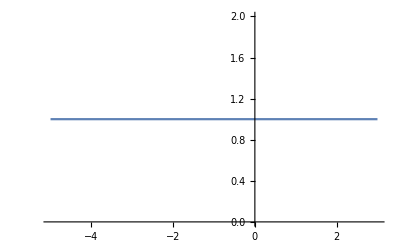

```mathematica
Plot[η[-Exp[-n]],{n,n0,nf}]
```

```mathematica
s=NDSolve[{x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]), x1[t0]==1, x2[t0]==0, y1[t0]==0, y2[t0]==0},{x1,x2,y1,y2},{t,t0,tf}];
```

```mathematica
s2=NDSolve[{x1'[t]==-ⅈ*η[t]/(k^3*t^3)*(D[cζ[t],t]*ζ[t]*y1[t]+D[cζ[t],t]*cζ[t]*y2[t]), x2'[t]==-ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*ζ[t]*y1[t]+-D[ζ[t],t]*cζ[t]*y2[t]),y1'[t]==ⅈ*η[t]/(k^3*t^3)*(-D[ζ[t],t]*cζ[t]*x1[t]+-D[cζ[t],t]*cζ[t]*x2[t]),
y2'[t]==ⅈ*η[t]/(k^3*t^3)*(D[ζ[t],t]*ζ[t]*x1[t]+D[cζ[t],t]*ζ[t]*x2[t]), x1[t0]==0, x2[t0]==0, y1[t0]==1, y2[t0]==0},{x1,x2,y1,y2},{t,t0,tf}];
```

```mathematica
xx1[t_]:=x1[t]/.s
xx2[t_]:=x2[t]/.s
yy1[t_]:=y1[t]/.s
yy2[t_]:=y2[t]/.s
```

```mathematica
xx11[t_]:=x1[t]/.s2
xx22[t_]:=x2[t]/.s2
yy11[t_]:=y1[t]/.s2
yy22[t_]:=y2[t]/.s2
```

```mathematica
P[t_]:=(Abs[xx1[t]+xx2[t]])^2 + (Abs[xx11[t]+xx22[t]])^2
```

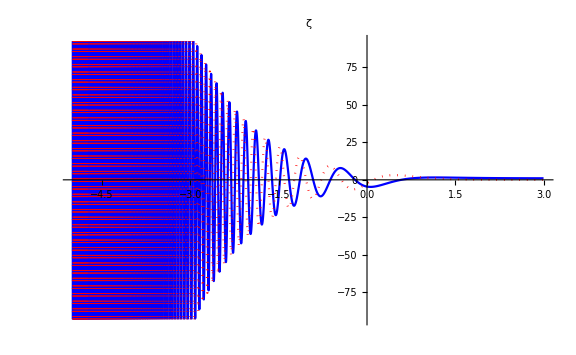

```mathematica
ReImPlot[ζ[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->ζ,ImageSize->Large]
```

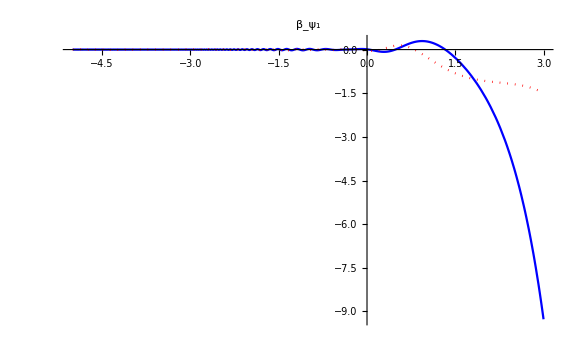

```mathematica
p4=ReImPlot[yy2[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[β, Subscript[ψ, 1]],ImageSize->Large, PlotRange->All]
```

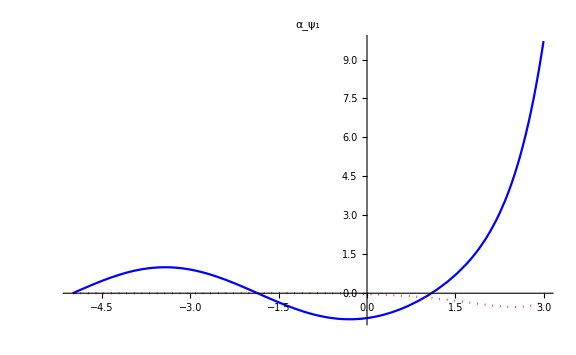

```mathematica
p3=ReImPlot[yy1[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[α, Subscript[ψ, 1]], ImageSize->Large, PlotRange->All]
```

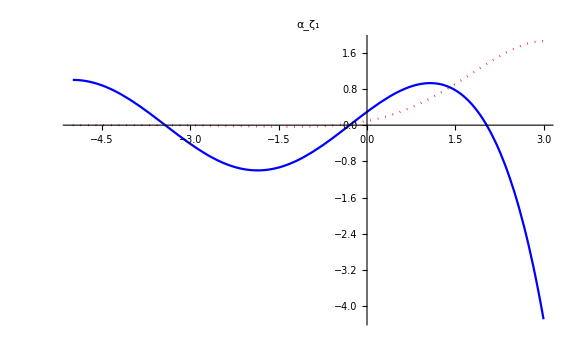

```mathematica
p1=ReImPlot[xx1[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[α, Subscript[ζ, 1]], ImageSize->Large, PlotRange->All]
```

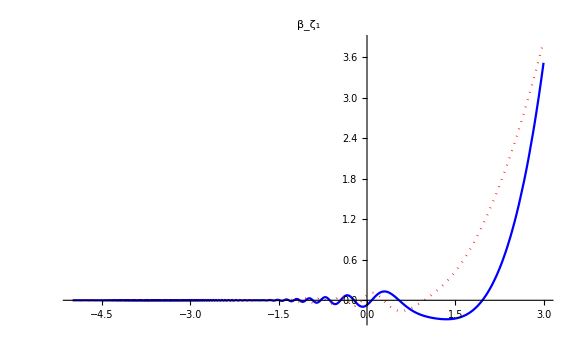

```mathematica
p2=ReImPlot[xx2[-Exp[-n]], {n,n0,nf}, ReImStyle->{Blue, Directive[Dashing, Red]}, PlotLabel->Subscript[β, Subscript[ζ, 1]], ImageSize->Large, PlotRange->All]
```

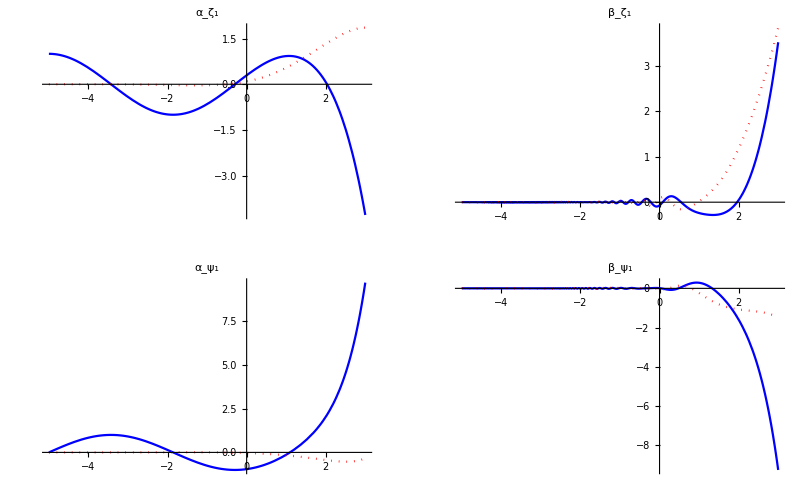

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}}, ImageSize->Full]
```

```mathematica
points1=Table[{n,yy2[-Exp[-n]]},{n,n0,nf,step}]
```

{{-5.,{0.+0. ⅈ}},{-4.9,{0.00138055-0.000276738 ⅈ}},{-4.8,{0.000122413-0.000798161 ⅈ}},{-4.7,{0.000693168+0.000693524 ⅈ}},{-4.6,{-0.000200243-0.000635257 ⅈ}},{-4.5,{-0.000399543-0.000263388 ⅈ}},{-4.4,{0.00128996-0.000825976 ⅈ}},{-4.3,{-0.000495413-0.000443888 ⅈ}},{-4.2,{-0.000333344+0.000562402 ⅈ}},{-4.1,{0.000174978+0.000891478 ⅈ}},{-4.,{0.000947447+0.000690675 ⅈ}},{-3.9,{0.000955805-0.000719669 ⅈ}},{-3.8,{-0.000409726+0.000424819 ⅈ}},{-3.7,{-0.000288849-0.000523106 ⅈ}},{-3.6,{-0.000354647-0.000040272 ⅈ}},{-3.5,{0.000254718-0.000059645 ⅈ}},{-3.4,{-0.000104047+0.0000545817 ⅈ}},{-3.3,{0.000292836-0.000268754 ⅈ}},{-3.2,{0.0000940956-0.000855384 ⅈ}},{-3.1,{0.00107608+0.000739659 ⅈ}},{-3.,{-0.000704141-0.0019537 ⅈ}},{-2.9,{-0.00159006-0.00238669 ⅈ}},{-2.8,{0.00278544-0.00156273 ⅈ}},{-2.7,{-0.00451877+0.00195497 ⅈ}},{-2.6,{0.00186544+0.00508375 ⅈ}},{-2.5,{0.0036425+0.00523846 ⅈ}},{-2.4,{-0.00279318+0.00760375 ⅈ}},{-2.3,{-0.00690098-0.00635203 ⅈ}},{-2.2,{0.00711759+0.00720331 ⅈ}},{-2.1,{-0.0005287-0.0117295 ⅈ}},{-2.,{-0.013999-0.00111644 ⅈ}},{-1.9,{-0.0126068+0.00919144 ⅈ}},{-1.8,{-0.013104+0.0110653 ⅈ}},{-1.7,{-0.0184281+0.00349105 ⅈ}},{-1.6,{-0.0128168-0.0151588 ⅈ}},{-1.5,{0.0159516-0.0127291 ⅈ}},{-1.4,{0.00387998+0.0219574 ⅈ}},{-1.3,{-0.018851-0.0142313 ⅈ}},{-1.2,{0.0222073+0.00803278 ⅈ}},{-1.1,{-0.0235421-0.00796489 ⅈ}},{-1.,{0.0190621+0.0148658 ⅈ}},{-0.9,{-0.00818835-0.0224385 ⅈ}},{-0.8,{-0.0114529+0.0198694 ⅈ}},{-0.7,{0.0205348+0.000724615 ⅈ}},{-0.6,{-0.00409054-0.0176345 ⅈ}},{-0.5,{-0.0145328+0.00315757 ⅈ}},{-0.4,{-0.00145938+0.0110463 ⅈ}},{-0.3,{0.00535722+0.00772141 ⅈ}},{-0.2,{0.0122665+0.00513436 ⅈ}},{-0.1,{0.0203035-0.00845978 ⅈ}},{0.,{0.0104206-0.0320693 ⅈ}},{0.1,{-0.0240467-0.0416521 ⅈ}},{0.2,{-0.0630989-0.0170952 ⅈ}},{0.3,{-0.0773396+0.0376338 ⅈ}},{0.4,{-0.0497456+0.0986385 ⅈ}},{0.5,{0.0166524+0.138223 ⅈ}},{0.6,{0.104246+0.137781 ⅈ}},{0.7,{0.190747+0.0919806 ⅈ}},{0.8,{0.256927+0.0063438 ⅈ}},{0.9,{0.29016-0.107676 ⅈ}},{1.,{0.284557-0.237188 ⅈ}},{1.1,{0.239324-0.370771 ⅈ}},{1.2,{0.156679-0.499772 ⅈ}},{1.3,{0.0400229-0.618498 ⅈ}},{1.4,{-0.107338-0.72381 ⅈ}},{1.5,{-0.282977-0.814508 ⅈ}},{1.6,{-0.485748-0.890729 ⅈ}},{1.7,{-0.71595-0.953461 ⅈ}},{1.8,{-0.975366-1.0042 ⅈ}},{1.9,{-1.26726-1.04472 ⅈ}},{2.,{-1.5964-1.07697 ⅈ}},{2.1,{-1.96908-1.103 ⅈ}},{2.2,{-2.39318-1.12498 ⅈ}},{2.3,{-2.87836-1.14525 ⅈ}},{2.4,{-3.43617-1.16631 ⅈ}},{2.5,{-4.08035-1.19097 ⅈ}},{2.6,{-4.82702-1.22235 ⅈ}},{2.7,{-5.69513-1.26403 ⅈ}},{2.8,{-6.70671-1.32009 ⅈ}},{2.9,{-7.88744-1.39525 ⅈ}},{3.,{-9.26706-1.49498 ⅈ}}}

```mathematica
nk=points1[[(nf-n0)/step]]
```

{2.9,{-7.88744-1.39525 ⅈ}}

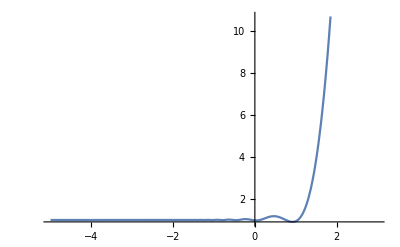

```mathematica
Plot[P[-Exp[-n]],{n,n0,nf}]
```